## Im(Self-energy)

```mathematica
Gauss[x_,μ_, width_, weight_]:=Module[{y},
σ=width/(Sqrt[2 Log[2]]);
y=weight/(σ*Sqrt[2π])Exp[-1/2((x-μ)/σ)^2]]
```

```mathematica
fs[x_]:=Gauss[x,0,0.05,1.0]
```

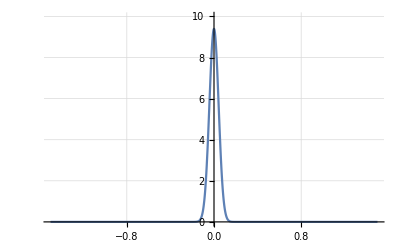

```mathematica
Plot[fs[x],{x,-1.5,1.5},PlotRange->{{-1.5,1.5},{0,10.0}},GridLines->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"Selfenergy.dat",Table[{ω,fs[ω]},{ω,-0.5,0.5,0.01}]]
```

\\Client\H$\Documents\acnotes\mbook\selfenergy\Selfenergy.dat

## A_0

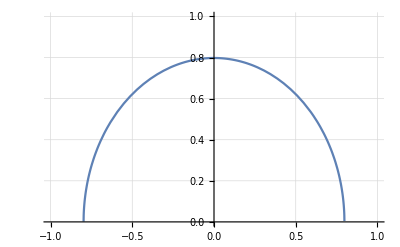

```mathematica
fa[x_]:=Sqrt[2.0/π-x^2]/;-Sqrt[2.0/π]≤x≤Sqrt[2.0/π];
fa[x_]:=0/;x≥Sqrt[2.0/π];
fa[x_]:=0/;x≤ -Sqrt[2.0/π];
Plot[fa[x],{x,-1,1},PlotRange->{{-1,1},{0,1.0}},GridLines->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"A0semicircle.dat",Table[{ω,fa[ω]},{ω,-1,1,0.01}]]
```

\\Client\H$\Documents\acnotes\mbook\selfenergy\A0semicircle.dat

```mathematica
f[x_]:=Sqrt[1.0/π-(x+2)^2]/;-2-Sqrt[1.0/π]≤x≤-2+Sqrt[1.0/π];
f[x_]:=Sqrt[1.0/π-(x-2)^2]/;2-Sqrt[1.0/π]≤x≤2+Sqrt[1.0/π];
f[x_]:=0/;x≥2+Sqrt[1.0/π];
f[x_]:=0/;x≤ -2-Sqrt[1.0/π];
f[x_]:=0/;-2+Sqrt[1.0/π]≤x≤ 2-Sqrt[1.0/π];
```

## Transform to Imaginary time

```mathematica
G[τ_,β_]:=NIntegrate[-fs[ω]Exp[-τ ω]/(1+Exp[-β ω]),{ω,-Infinity,Infinity}]
β=50.;
Ntau=1000;
```

```mathematica
TabulatedG=Table[{β/Ntau*n,G[β/Ntau*n,β]},{n,0,Ntau}];
```

```mathematica
Export[NotebookDirectory[]<>"SelfenergyTime.dat",TabulatedG]
```

\\Client\H$\Documents\acnotes\mbook\selfenergy\SelfenergyTime.dat

## Kramers Kronig Relation

```mathematica
nmax=1000
```

```mathematica
ωtable=Import[NotebookDirectory[]<>"x.dat","List"];
```

```mathematica
ImSigmatable=Import[NotebookDirectory[]<>"f.dat""List"];
```

```mathematica
data=Import[NotebookDirectory[]<>"data.dat","Table"];
ff=Interpolation[data];
Plot[ff[x],{x,First[data][[1]],Last[data][[1]]}]
N
Integrate[f[x],{x,First[data][[1]],Last[data][[1]]}]
```

```mathematica
ReSigmatable=Table[NIntegrate[ImSigmatable[[i]]/(ωtable[[j]]-ωtable[[i]]),{i,1,nmax}],{j,1,nmax}];
```

```mathematica
ωReSigmatable=Table[{ωtable[[j]],ReSigmatable[[j]]},{j,1,nmax}];
```

```mathematica
Export[NotebookDirectory[]<>"ReSigma.dat",ωReSigmatable]
```

\\Client\C$\Users\tchen\Documents\acnotes\mbook\imaginary\TripleGaussianFrequency.dat

```mathematica
"/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat"
```

/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat

## Transform to Matsubara Frequency

```mathematica
nmax=1000
```

1000

```mathematica
iωntable=Table[I(2n+1)π/β,{n,1,nmax}];
```

```mathematica
Giωntable=Table[NIntegrate[TripleCurve[ω]/(iωntable[[j]]-ω),{ω,-Infinity,Infinity}],{j,1,nmax}];
```

```mathematica
ωnReGiωntable=Table[{Im[iωntable[[j]]],Re[Giωntable[[j]]]},{j,1,nmax}];
ωnImGiωntable=Table[{Im[iωntable[[j]]],Im[Giωntable[[j]]]},{j,1,nmax}];
```

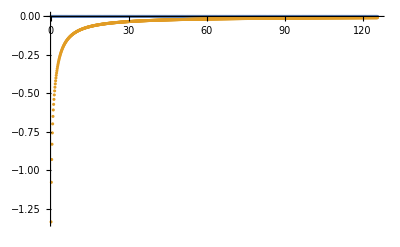

```mathematica
ListPlot[{ωnReGiωntable,ωnImGiωntable},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"TripleGaussianFrequency.dat",ωnImGiωntable]
```

\\Client\C$\Users\tchen\Documents\acnotes\mbook\imaginary\TripleGaussianFrequency.dat

```mathematica
"/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat"
```

/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat